```mathematica
AlphaMin=0.00;
AlphaMax=1.00;
AlphaInterval=0.01;
```

```mathematica
AlphaMin=0.10;
AlphaMax=0.29;
AlphaInterval=0.01;
gfacMin=-10.;
gfacMax=9.;
gfacInterval=1.;
nocc=1;
c0=1.0;
c1=0.5;
Table[
Table[
Table[
res[gfac][nbas][omega][alpha][c0][c1]= ReadList["/home/grining/drake-mpfun/python/results/nocc="<>ToString[nocc]<>"nbas="<>ToString[nbas]<>"omega="<>ToString[omega]<>"gfac="<>ToString[NumberForm[gfac, {2,2}]]<>"alpha="<>ToString[NumberForm[alpha, {2,2}]]<>"c0="<>ToString[NumberForm[c0, {2,2}]]<>"c1="<>ToString[NumberForm[c1, {2,2}]]<>".out_FCCD"][[1]]
,{gfac, gfacMin, gfacMax,gfacInterval}];
,{nbas, {9}}];
,{omega,{9}},
{alpha,AlphaMin,AlphaMax,AlphaInterval}];
```

```mathematica
Table[
ResVsAlpha[g]=Table[{alpha, res[g][9][9][alpha][1.00][0.50]}, {alpha,AlphaMin,AlphaMax,AlphaInterval}],
{g, gfacMin, gfacMax,gfacInterval}];
```

```mathematica
Table[First@SortBy[ResVsAlpha[g],#[[2]]&],{g,  gfacMin, gfacMax,gfacInterval}]
```

{{0.2,-28.868003067094222427659182515197965527962},{0.2,-21.6742854122629712927970497010558730977},{0.24,-33.905440523903196215228843296331718390376},{0.25,-20414.034541195553151554610428336687978432044},{0.27,-17.127658591347318465708288551692463445179},{0.29,-8.947286025484318468611507142717837207327},{0.29,-3.820083607856000187517933530742462559378},{0.29,-1.657870143431593194632878877770100069018},{0.29,-0.374889926989646311317639707555312304445},{0.29,0.472684063016477718408845032163206327238},{0.1,1.},{0.2,1.306858372203681456995694365315959039145},{0.2,1.489160859849137410773898564244218029315},{0.22,1.607354037067458454394942187220365996993},{0.21,1.69277522984087410969092347292909464272},{0.2,1.760975647005053648506712405520049191033},{0.11,1.820417049248772743541833897648219200421},{0.14,4.000467101469413415606022945076857871291},{0.23,1.926629669492607277427506177880922443722},{0.27,-829.045605814309528592432890443669714197577}}

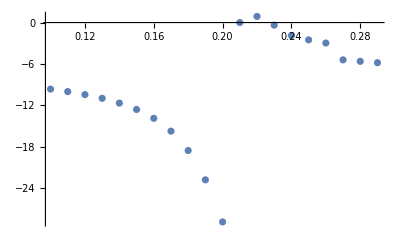
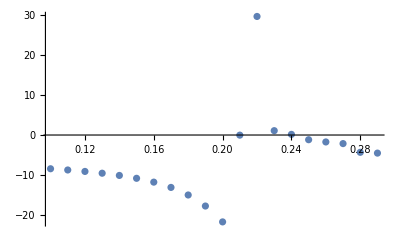
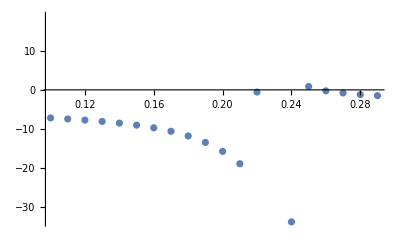
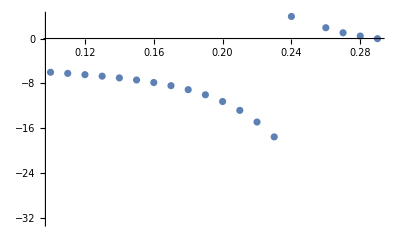
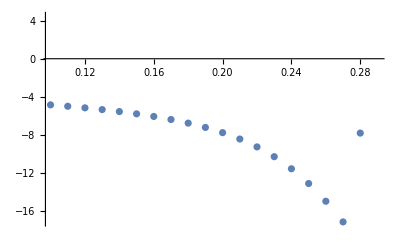
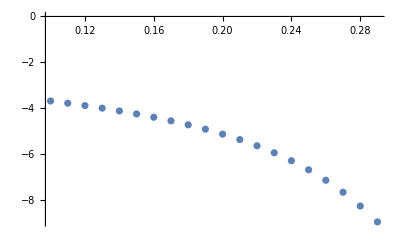
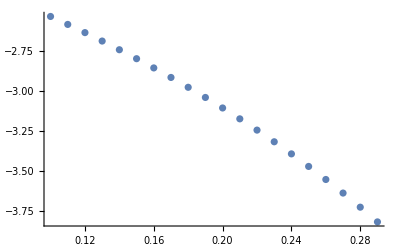
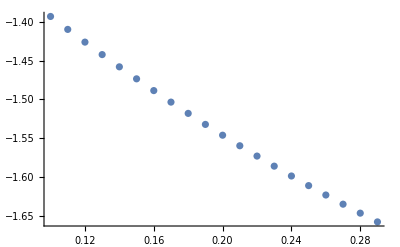

```mathematica
Table[ListPlot[ResVsAlpha[g],ImageSize->400],{g, gfacMin, gfacMax,gfacInterval}]
```